```mathematica
SetDirectory["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\Thermal Conductivity\\Программа\\ThermalConductivity"];
```

```mathematica
data=Import["test.txt", "Table"];
l=data[[1,1]];
x=Table[i*l/(Length@data[[2]]-1),{i,0,Length@data[[2]]-1}];
data=Delete[data,1];
MinMax[data]
```

{0,5}

Эволюция решения на протяжении всего решения

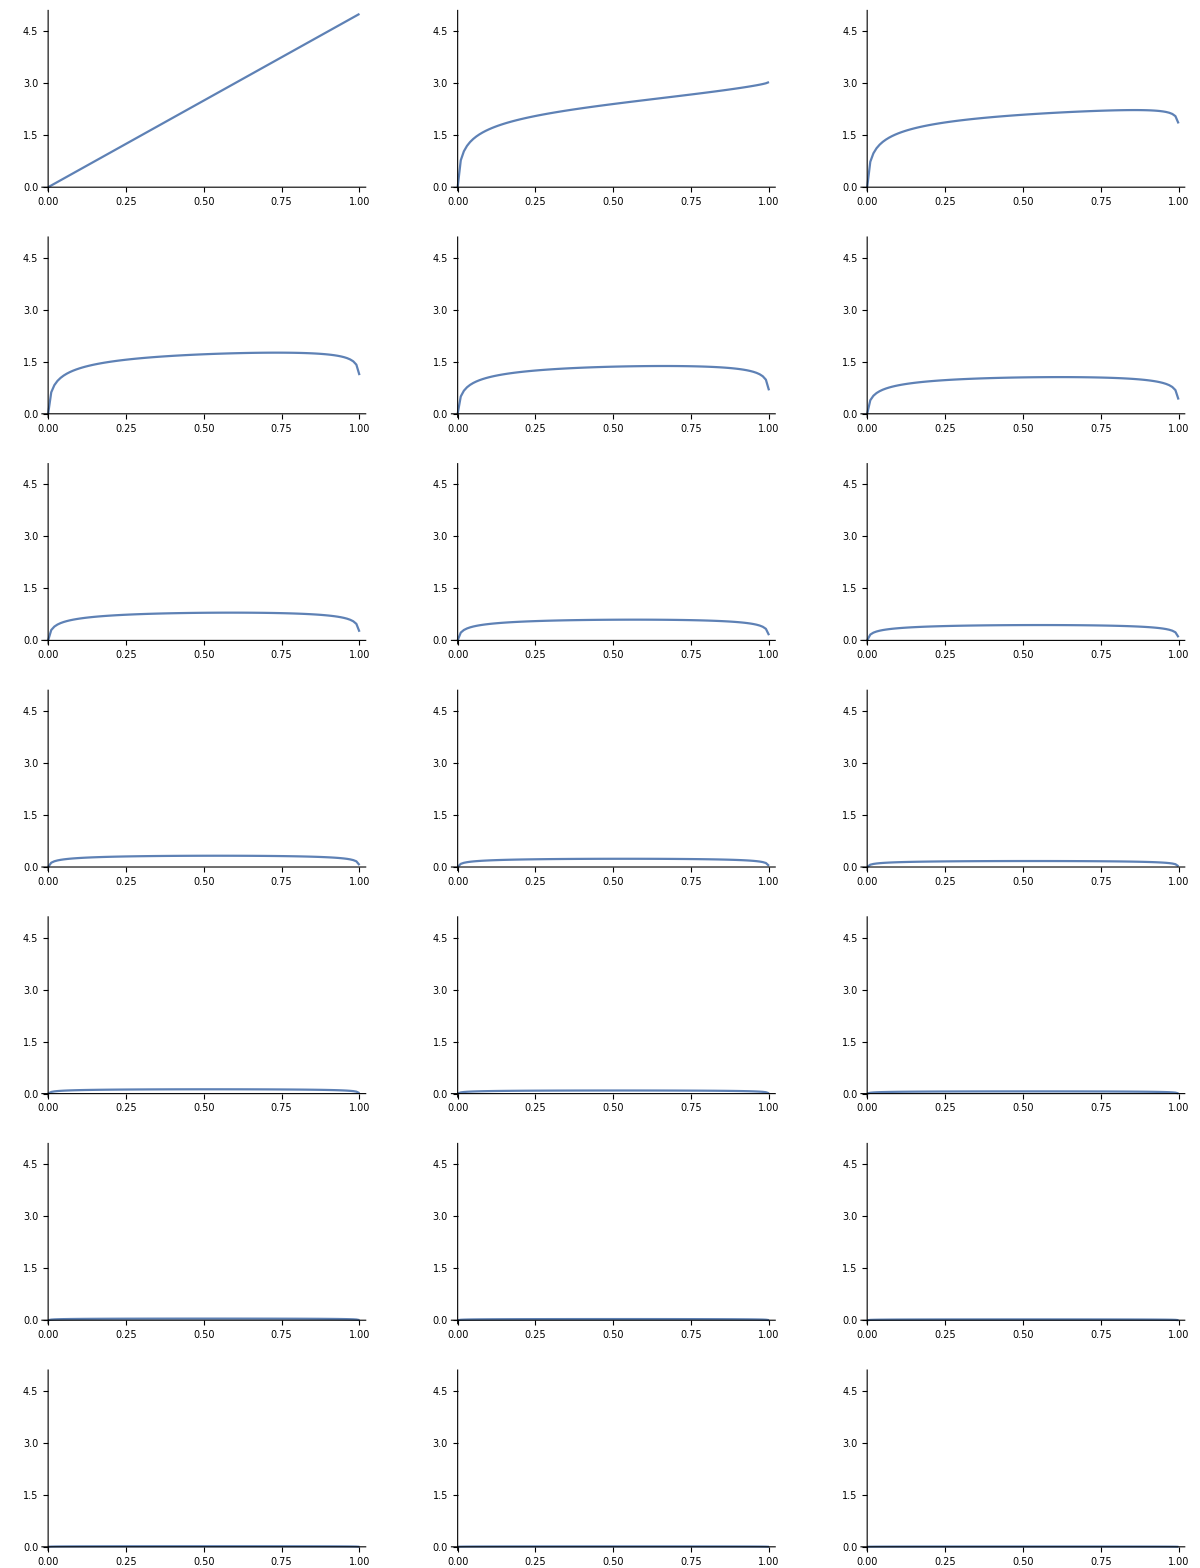

```mathematica
GraphicsGrid@Partition[Map[ListLinePlot[MapIndexed[{el,i}|->{x[[First@i]],el},#],PlotRange->{{0,Last@x},MinMax@data}]&,data[[;;;;50]]],UpTo[3]]
```

Эволюция решения в начальные моменты времени

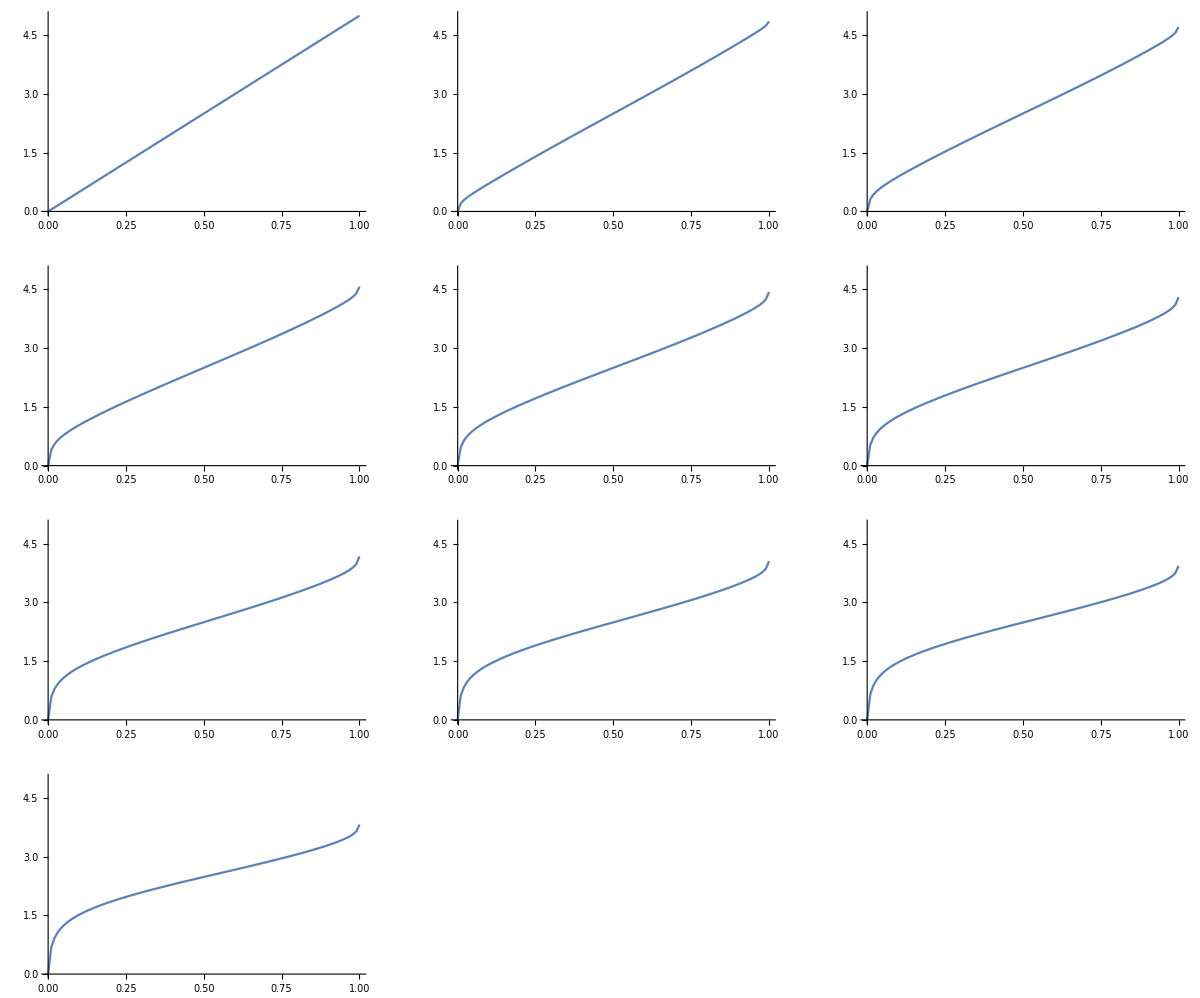

```mathematica
maxTime=30;
GraphicsGrid@Partition[Map[ListLinePlot[MapIndexed[{el,i}|->{x[[First@i]],el},#],PlotRange->{{0,Last@x},MinMax@data[[;;maxTime]]}]&,data[[;;maxTime;;3]]],UpTo[3]]
```

### Тестовая задача

```mathematica
A=5;
a[x_]:=√Sin[π/l x]
```

```mathematica
u[x_,t_]:=(A x)/l Exp[-t]+(2A l^2)/π Sum[((-1)^n(Exp[-((n π)/l)^2 a[x]^2 t]-Exp[-t]))/(n(n^2 π^2 a[x]^2-l^2))Sin[(n π x)/l],{n,1,∞}]
```

```mathematica
Plot[u[x,t],{x,0,l}]
```